```mathematica
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["FunctionApproximations`"];

ClearAll[k,s,m,λ,A,B,Rhor,L,a,rp,rm,kH,Omega,Mw,M,astar,w,apb,amb,H,f0,f1,f2,f3,f4,f5,f6,term1,term2,term3,Elm,λ0,QQ,CC,ϵ];
s=-2;
(****************** Common prameters *************************)
rp=1;
M=rp/(1+Sqrt[1-astar^2]);
a=M*astar;
kH=1/(2*M*(1+(1-astar^2)^(-1/2)));
Omega=astar/(2*M*(1+(1-astar^2)^(1/2)));

m=2+10^(-17);
L=2+10^(-17);

astarmax=0.5;
Mmax=rp/(1+Sqrt[1-astarmax^2]);
Omegamax=astarmax/(2*Mmax*(1+(1-astarmax^2)^(1/2)));

astar=0.5;
startw=0.01*m*Mmax*Omegamax;
Nw=110;

(****************  precision parameters  ***************************)
dMw=0.01*m*Mmax*Omegamax;
r0=1+10^(-4);
startstep=10^(-6);
rmax=1000;
stepmax=1;
plotrmax=1000;
numsteps=Infinity;

(*****************  angular eigenvalues Elm ***********************)
mm:=m;
apb:=Max[Abs[mm],Abs[s]];

amb:=mm*s/apb;

H[L_]:=(L^2-apb^2)*(L^2-s^2)*(L^2-amb^2)/2/(L-1/2)/L^3/(L+1/2);
f0:=L*(L+1);
f1:=-2*s^2*mm/L/(L+1);
f2:=H[L+1]-H[L]-1;
f3:=2*s^2*mm*(H[L]/(L-1)/L^2/(L+1)-H[L+1]/(L+2)/(L+1)^2/L);
f4:=4*s^4*mm^2*(H[L+1]/(L+2)^2/(L+1)^4/L^2-H[L]/(L-1)^2/L^4/(L+1)^2)+1/2*(H[L+1]^2/(L+1)+H[L+1]*H[L]/(L+1)/L-H[L]^2/L)+1/4*((L-1)*H[L]*H[L-1]/L/(L-1/2)-(L+2)*H[L+1]*H[L+2]/(L+1)/(L+3/2));

f5:=8*s^6*mm^3*(H[L]/(L-1)^3/L^6/(L+1)^3-H[L+1]/(L+2)^3/(L+1)^6/L^3)+s^2*mm*(3*H[L]^2/(L-1)/L^3/(L+1)-(7*L^2+7*L+4)*H[L]*H[L+1]/(L-1)/L^3/(L+1)^3/(L+2)-3*H[L+1]^2/(L+2)/(L+1)^3/L+1/2*((3*L+7)*H[L+1]*H[L+2]/(L+3)/(L+3/2)/(L+1)^3/L-(3*L-4)*H[L]*H[L-1]/(L-2)/(L-1/2)/L^3/(L+1)));

term1:=16*s^8*mm^4*(H[L+1]/(L+2)^4/(L+1)^8/L^4-H[L]/(L-1)^4/L^8/(L+1)^4);
term2:=4*s^4*mm^2*(3*H[L+1]^2/(L+2)^2/(L+1)^5/L^2+(11*L^4+22*L^3+31*L^2+20*L+6)*H[L]*H[L+1]/(L-1)^2/L^5/(L+1)^5/(L+2)^2-3*H[L]^2/(L-1)^2/L^5/(L+1)^2+1/2*((3*L^2-8*L+6)*H[L]*H[L-1]/(L-2)^2/(L-1)/(L-1/2)/L^5/(L+1)^2-(3*L^2+14*L+17)*H[L+1]*H[L+2]/(L+3)^2/(L+2)/(L+3/2)/(L+1)^5/L^2));
term3:=1/4*(2*H[L+1]^3/(L+1)^2+(2*L^2+4*L+3)*H[L]^2*H[L+1]/L^2/(L+1)^2-(2*L^2+1)*H[L+1]^2*H[L]/(L+1)^2/L^2-2*H[L]^3/L^2+(L+2)*(3*L^2+2*L-3)*H[L]*H[L+1]*H[L+2]/4/(L+3/2)^2/(L+1)^2/L-(L-1)*(3*L^2+4*L-2)*H[L+1]*H[L]*H[L-1]/4/(L-1/2)^2/L^2/(L+1)+(L+2)^2*H[L+2]^2*H[L+1]/4/(L+3/2)^2/(L+1)^2-(L-1)^2*H[L-1]^2*H[L]/4/(L-1/2)^2/L^2+(L-1)*(7*L-3)*H[L]^2*H[L-1]/4/(L-1/2)^2/L^2-(L+2)*(7*L+10)*H[L+1]^2*H[L+2]/4/(L+3/2)^2/(L+1)^2+(L+3)*H[L+1]*H[L+2]*H[L+3]/12/(L+3/2)^2/(L+1)-(L-2)*H[L]*H[L-1]*H[L-2]/12/(L-1/2)^2/L);
f6:=term1+term2+term3;


Elm:=N[f0]+N[f1]*a*w+N[f2]*a^2*w^2+N[f3]*(a*w)^3+N[f4]*(a*w)^4+N[f5]*(a*w)^5+N[f6]*(a*w)^6;
λ:=-(-2)*(-2+1)+a^2*w^2+Elm;
λ0:=-2*(2+1)+a^2*w^2+Elm; (* this is the λ for s=2, useful for CC *)

(****************** ODE functions **********************************)
Tri[r_]:=r^2-2*M*r+a^2;
x[r_]:=r+2*M/(rp-rm)*(rp*Log[r-rp]-rm*Log[r-rm]);
k=w-m*Omega;


A[r_]:=-(s+1)Tri'[r]/Tri[r];

B[r_]:=-((r^2+a^2)^2*w^2 - 4 a M r w m + a^2*m^2 + 2 I a (r-M) m s - 2 I M (r^2-a^2) w s + (2 I r w s-λ) Tri[r])/Tri[r]^2;


Rhor[r_]:=Tri[r]^(-s)*Exp[-I*k*x[r]];

QQ=2*(2+1)+λ0-2*a*m*w;
CC=Sqrt[(QQ^2+4*a*m*w-4*a^2*w^2)*((QQ-2)^2+36*a*m*w-36*a^2*w^2)+(2*QQ-1)*(96*a^2*w^2-48*a*w*m)+144*w^2*(M^2-a^2)];
list1=startw+dMw*(Range[1,Nw]-1);
list3=Table[y,{y,1,Nw}];
```

```mathematica
(*************** Use R to get A ******************)
rm=M^2*astar^2;
For[i=1,i≤Nw,i++,
Mw=startw+dMw*(i-1);
w=Mw/M;
thermal=1;
solR2=NDSolve[{Rm''[r]==A[r]*Rm'[r]+B[r]*Rm[r],Rm[r0]==Rhor[r0],Rm'[r0]==Rhor'[r0]},Rm,{r,r0,rmax},StartingStepSize->startstep,Method->{"StiffnessSwitching"},AccuracyGoal->10,MaxSteps->numsteps,MaxStepSize->stepmax];

ϵ=Sqrt[M^2-a^2]/(4*M);
list3[[i]]=thermal*(128*w*k*(k^2+4*ϵ^2)*(k^2+16*ϵ^2)*(2*M)^5/CC^2)/(1/(2*w^2)*(1/rmax^3*Abs[Evaluate[Rm[rmax]/.solR2]])^2+128*w*k*(k^2+4*ϵ^2)*(k^2+16*ϵ^2)*(2*M)^5/CC^2);]
```

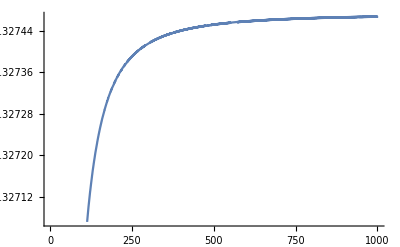

```mathematica
Plot[Abs[Rm[r]/.solR2]/r^3,{r,r0,rmax}]
```